```mathematica
Integrate[(Cos[x])^2,{x,0,2*π}]
```

π

```mathematica
Integrate[(Cos[x]*Cos[x+t]),{x,0,2 π}]
```

π Cos[t]

```mathematica
c = 29.1;
b = c*(1+ⅈ)
Conjugate[(1-b)/(1+b)]*((1-b)/(1+b))
```

29.1+29.1 ⅈ

0.933593+0. ⅈ

```mathematica
a = Cos[ArcSin[2/3*Sin[t]]]/Cos[t];
fT[t_]:=2/(1+3/2*a);
fR[t_]:=Abs[(1-1.5*a)/(1+1.5*a)];
```

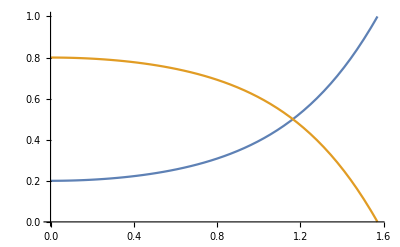

```mathematica
Plot[{fR[t],fT[t]},{t,0,π/2}]
```